A novel solution to the Klein–Gordon equation in the presence of a strong rotating electric field

E. Raicher, S. Eliezer, A. Zigler, Physics Letters B 750 (2015) 76–81
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

## Equation 9: expansion as Fourier series

```mathematica
Clear[y,z,n,c2n,μ,λ,q,eq6]
y[z]=Exp[I μ z]Sum[c2n[n] Exp[2I z n],n]
eq6=D[y[z],{z,2}]+(λ-2q (Exp[I 2z]+Exp[-I 2z])/2)y[z]//FullSimplify
```

ⅇ^(ⅈ z μ) ∑_n ⅇ^(2 ⅈ n z) c2n[n]

ⅇ^(ⅈ z μ) ((λ-μ^2-2 q Cos[2 z]) ∑_n ⅇ^(2 ⅈ n z) c2n[n]+2 ⅈ μ ∑_n 2 ⅈ ⅇ^(2 ⅈ n z) n c2n[n]+∑_n -4 ⅇ^(2 ⅈ n z) n^2 c2n[n])

```mathematica
Solve[eq6]
```

## Equation 19: solving analytically 1st order equation

```mathematica
Clear[λ,y,z,q]
DSolve[{y'[z]+I(Sqrt[λ]-q/Sqrt[λ] Cos[2z])y[z]==0},y[z],z]//Simplify
```

{{y[z]→ⅇ^(-(ⅈ (z λ-q Cos[z] Sin[z]))/(√λ)) C[1]}}

## Equation 22: Bessel function expansion

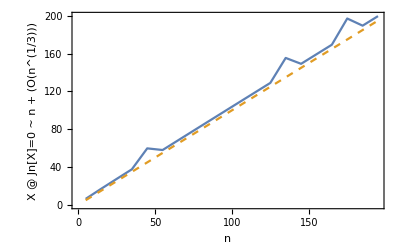

```mathematica
(* first maximum @ X~n *)
Clear[n,X,root]
root[n_]:=(FindMaximum[BesselJ[n,X],{X,0.9n}]//Quiet)[[2,1,2]]
ListPlot[{ParallelTable[{n,root[n]},{n,5,200,10}],ParallelTable[{n,n},{n,5,200,10}]},Joined->True,Frame->True,FrameLabel->{"n","X @ Jn[X]=0 ~ n + (O(n^(1/3)))"},PlotStyle->{Default,Dashed}]
```

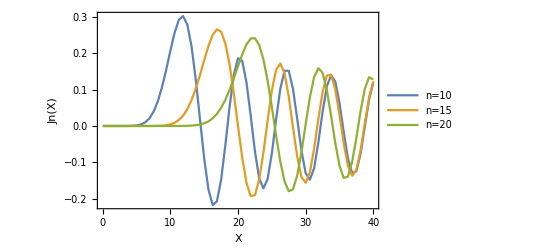

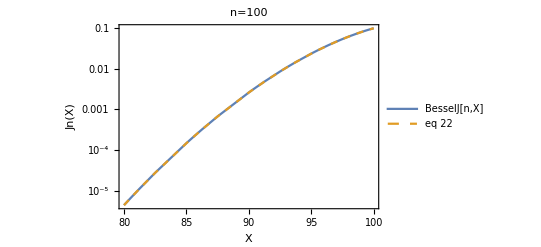

```mathematica
Clear[n,X,tanhα]
Plot[{BesselJ[10,X],BesselJ[15,X],BesselJ[20,X]},{X,0,40},PlotPoints->2,Frame->True,FrameLabel->{"X","Jn(X)"},PlotLegends->{"n=10","n=15","n=20"}]

n=100;
tanhα=Sqrt[1-(X/n)^2];
LogPlot[{BesselJ[n,X],tanhα/(π √3)BesselK[1/3,1/3 n tanhα^3]Exp[n(tanhα+1/3 tanhα^3-ArcTanh[tanhα])]},{X,0.8n,n},PlotStyle->{Default,Dashed},PlotPoints->2,Frame->True,FrameLabel->{"X","Jn(X)"},PlotLegends->{"BesselJ[n,X]","eq 22"},PlotLabel->"n=100"]
```

## Equation 24: simple Taylor series

```mathematica
Clear[α]
Series[Tanh[α]+1/3 Tanh[α]^3-α,{α,0,6}]
```

-α^5/5+O[α]^7

## Equation 25: simple K1/3 expansion

```mathematica
Clear[u]
Series[BesselK[1/3,u],{u,0,0}]
```

Gamma[1/3]/(2^(2/3) u^(1/3))+O[u]^(1/3)

## Figure 1

parameters for figure 1:

δ=0.0199461

Ω=19.271

ν=189.878

νV=1924.5

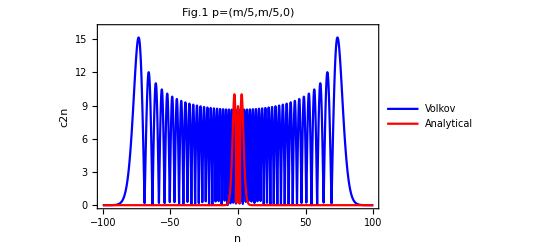

```mathematica
(* figure 1: *)
Clear[ea,m,p0,pprp,p,ξ,mph,ν,nstar,pdotϵ,kdotp,nstar,nstarV,ν,νV]
(* "definitions" equation 52 *)
δ=(√2 ea pprp)/(p0^2+ea^2);
Ω=Sqrt[1+(ea/p0)^2];
(* in these units *)
m=1;
ea=20 m;
(* 3-vector momentum *)
p={m/5,m/5,0};
(* 0 component in 4-momentum *)
p0=Refine[Sqrt[1+Norm[p]^2],{m>0}];
(* as in main text *)
δ=δ/.{pprp->Norm[p]}//N;
Ω=Ω//N;

ξ=20;
mph=m/10;
kdotp=p0 mph;
(* equation 51 *)
pdotϵ=pprp/(√2)/.{pprp->Norm[p]}//N;
(* eq 34: new analytical solution *)
nstar=(ea pdotϵ)/(Ω kdotp)//N;
ν=kdotp/mph^2(Ω-1)//N;
nstarV=(ea pdotϵ)/kdotp//N;
νV=ea^2/(2kdotp)//N;

Print["parameters for figure 1:"]
Print["δ=",δ]
Print["Ω=",Ω]
Print["ν=",ν]
Print["νV=",νV]
Plot[{9.5 10^-4 10^5 Abs[BesselJ[n//Abs,2nstarV]],2.25 10^-4 10^5 Abs[BesselJ[n//Abs,2nstar]]},{n,-100,100},PlotRange->{0,16},Frame->True,FrameLabel->{"n","c2n"},PlotStyle->{Blue,Red},PlotLegends->{"Volkov","Analytical"},PlotLabel->"Fig.1 p=(m/5,m/5,0)"]
```

## Figure 2

parameters for figure 2:

δ=0.443459

Ω=2.97374

ν=140.953

νV=280.056

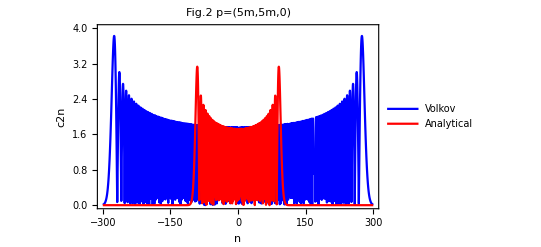

```mathematica
(* figure 2: *)
Clear[ea,m,p0,pprp,p,ξ,mph,ν,nstar,pdotϵ,kdotp,nstar,nstarV,ν,νV,δ,Ω]
(* "definitions" equation 52 *)
δ=(√2 ea pprp)/(p0^2+ea^2);
Ω=Sqrt[1+(ea/p0)^2];
(* in these units *)
m=1;
ea=20 m;

p={5m,5m,0};
(* 0 component in 4-momentum *)
p0=Refine[Sqrt[1+Norm[p]^2],{m>0}];
(* as in main text *)
δ=δ/.{pprp->Norm[p]}//N;
Ω=Ω//N;

ξ=20;
mph=m/10;
kdotp=p0 mph;
(* equation 51 *)
pdotϵ=pprp/(√2)/.{pprp->Norm[p]}//N;
(* eq 34: new analytical solution *)
nstar=(ea pdotϵ)/(Ω kdotp)//N;
ν=kdotp/mph^2(Ω-1)//N;
nstarV=(ea pdotϵ)/kdotp//N;
νV=ea^2/(2kdotp)//N;

Print["parameters for figure 2:"]
Print["δ=",δ]
Print["Ω=",Ω]
Print["ν=",ν]
Print["νV=",νV]
Plot[{3.7 10^-4 10^5 Abs[BesselJ[n//Abs,2nstarV]],2.1 10^-4 10^5 Abs[BesselJ[n//Abs,2nstar]]},{n,-300,300},PlotRange->{0,4},Frame->True,FrameLabel->{"n","c2n"},PlotStyle->{Blue,Red},PlotLegends->{"Volkov","Analytical"},PlotLabel->"Fig.2 p=(5m,5m,0)"]
```